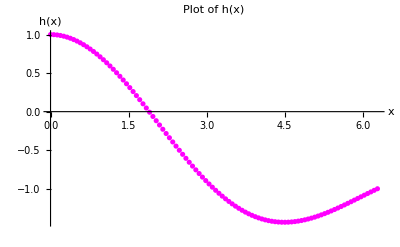

```mathematica
h[x_] := (2Sinc[x])-1
Points := Subdivide[0,2Pi,99] 
ListPlot[Transpose[{Points,h[Points] }],PlotStyle->Magenta,AxesLabel->{"x","h(x)"},PlotLabel-> "Plot of h(x)"]
```

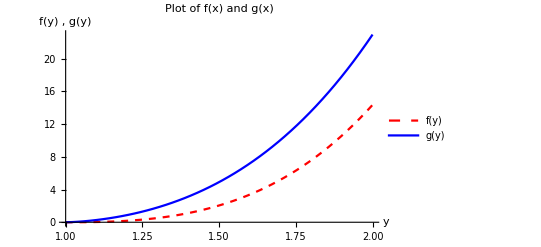

```mathematica
f[y_]:= y(2 y^2-5)(y^2-1)^(1/2)+3Log[y+(y^2-1)^(1/2)]
g[y_]:= y(2 y^2-1)(y^2-1)^(1/2)-Log[y+(y^2-1)^(1/2)]

Plot[{f[y],g[y]},{y,1,2}, PlotStyle->{{Dashed,RGBColor[1,0,0]},RGBColor[0,0,1]},PlotLegends -> "Expressions", PlotLabel -> "Plot of f(x) and g(x)" ,AxesLabel->{"y","f(y) , g(y)"}]
```

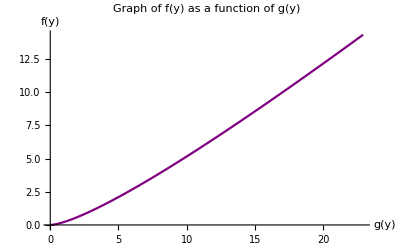

```mathematica
ParametricPlot[{g[y],f[y]},{y,1,2}, PlotStyle->Purple,  PlotLabel -> "Graph of f(y) as a function of g(y)", AxesLabel->{"g(y)","f(y)"} ]
```

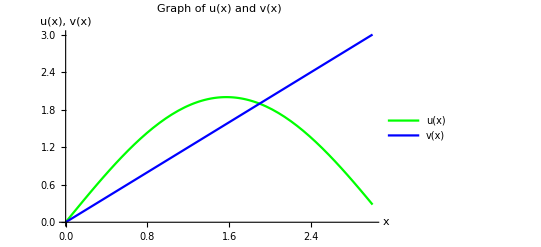

```mathematica
u[x_]:=2Sin[x]
v[x_]:=x
Plot[{u[x],v[x]},{x,0,3}, PlotStyle->{RGBColor[0,1,0],{"Dashed",RGBColor[0,0,1]}},PlotLabel -> "Graph of u(x) and v(x)", AxesLabel->{"x","u(x), v(x)"},PlotLegends->"Expressions"]
```